```mathematica
(* Subscript[I, 2](l,L) at 2 T_c with free b.c.
=c/2 ln[(f(l/L) f((L-l)/L))/(√L f(1))]
where f(x)=Dedekindeta(ix) *)
```

```mathematica
(* Subscript[I, 2](l,L)-Subscript[I, 2](L/2,L) *)
Log[F[x,L]]-Log[F[1/2,L]]//FullSimplify
```

Log[L]/2+Log[(DedekindEta[-ⅈ (-1+x)] DedekindEta[ⅈ x])/(√L DedekindEta[ⅈ/2]^2)]

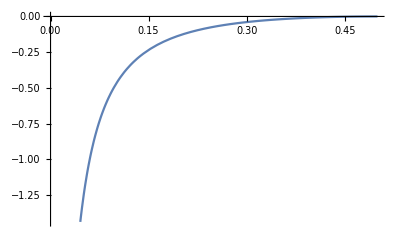

```mathematica
Clear[J,l,L,x,F,c];
(* for classical Blume-Capel model *)
c=7/10;
F[x_]:=(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2;
p=Plot[c/2 Log[F[x]],{x,0,0.5}]
```

```mathematica
(* fit data *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
dm8=Import["MI2_L8_B0.82101"];
dm16=Import["MI2_L16_B0.82101"];
b8=dm8[[;;,1]];
b16=dm16[[;;,1]];
d8=Transpose[{b8,b8}]
d16=Transpose[{b16,b16}]
```

Import::fmterr: Cannot import data as "BYU" format.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

{{-2.07236,-2.07236},{-0.387396,-0.387396},{-0.110147,-0.110147},{-0.02205,-0.02205},{0.,0.},{-0.02205,-0.02205},{-0.110147,-0.110147},{-0.387396,-0.387396},{-2.07236,-2.07236}}

Transpose::nmtx: The first two levels of the one-dimensional list {Symbol[], Symbol[]} cannot be transposed.

Transpose[{Symbol[],Symbol[]}]

{c→0.307007}

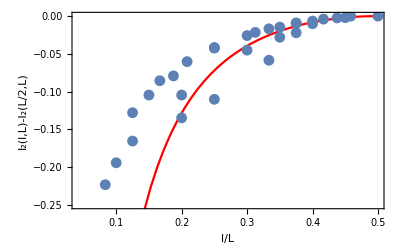

```mathematica
datanew={{1/6,-0.30905443},{2/6,-0.05843671},{1/8,-0.38739597},{2/8,-0.11014749},{3/8,-0.02205001},{4/8,0},
{1/10,-0.41925040},{2/10,-0.13474265 },{3/10,-0.04504970},{4/10,-0.01002948},{1/16,-0.47048348},{2/16,-0.16540133},{3/16,-0.07915012},{4/16,-0.04189553},{5/16,-0.02155202},{6/16,-0.00947486},{7/16,-0.00235248},{1/20,-0.51643542},{2/20,-0.19417424},{3/20,-0.10450639},{4/20,-0.10450639},{5/20,-0.04190940},{6/20,-0.02572357},{7/20,-0.01456808},{8/20,-0.00656855},{9/20,-0.00205329},{1/24,-0.56884936},{2/24,-0.22323951},{3/24,-0.12787162},{4/24,-0.08552056},{5/24,-0.06024982},{6/24,-0.04203786},{7/20,-0.02800167},{8/24,-0.01678355},{9/24,-0.00901948},{10/24,-0.00396543},{11/24,0}};
lnew=ListPlot[datanew];
(*******************)
Clear[J,x,F,c,pfit,pactual];
Jstephen[c_,x_]:=c Log[Sin[x π]];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ/2]^2];
fit=FindFit[datanew,J[c,x],{c},x]
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Red}];
Show[pactual,lnew,PlotRange->{-0.25,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"}]
```

{c→1.6214}

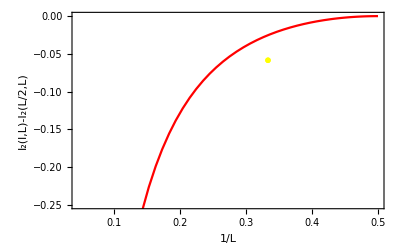

{c→0.84142}

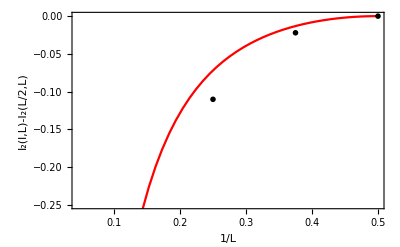

{c→0.629362}

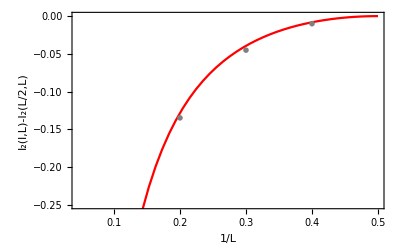

{c→0.350451}

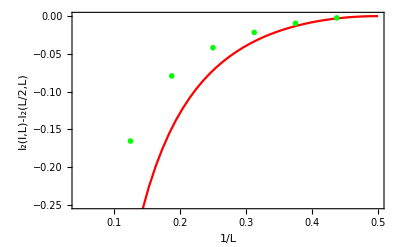

{c→0.288266}

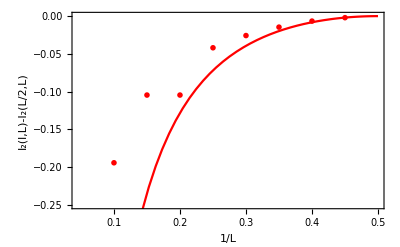

{c→0.250502}

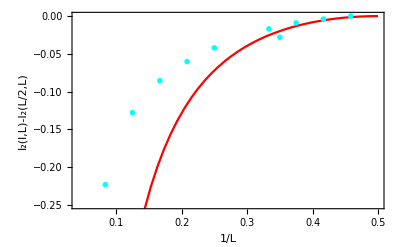

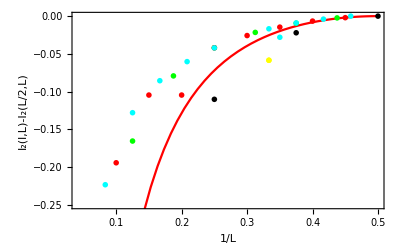

```mathematica
(* without (l=1)/L data point*)
SetDirectory[NotebookDirectory[]];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Red}];
(***************)
marker1=Graphics[{Disk[]}];
data6={{2/6,-0.05843671}};
l6=ListPlot[data6,PlotStyle->Yellow,PlotMarkers->{marker1,.03}];
fit6=FindFit[data6,J[c,x],{c},x]
Show[pactual,l6,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=6"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
data8={{1/8,-0.38739597},{2/8,-0.11014749},{3/8,-0.02205001},{4/8,0}};
l8=ListPlot[data8,PlotStyle->Black,PlotMarkers->{marker1,.03}];
fit8=FindFit[data8,J[c,x],{c},x]
Show[pactual,l8,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=8"}}]
(*aaaaaaaaaaaaaaaaaaaaa*)
data10={{1/10,-0.41925040},{2/10,-0.13474265 },{3/10,-0.04504970},{4/10,-0.01002948}};
l10=ListPlot[data10,PlotStyle->Gray,PlotMarkers->{marker1,.03}];
fit10=FindFit[data10,J[c,x],{c},x]
Show[pactual,l10,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=10"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
data16={{1/16,-0.47048348},{2/16,-0.16540133},{3/16,-0.07915012},{4/16,-0.04189553},{5/16,-0.02155202},{6/16,-0.00947486},{7/16,-0.00235248}};
l16=ListPlot[data16,PlotStyle->Green,PlotMarkers->{marker1,.03}];
fit16=FindFit[data16,J[c,x],{c},x]
Show[pactual,l16,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=16"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
data20={{1/20,-0.51643542},{2/20,-0.19417424},{3/20,-0.10450639},{4/20,-0.10450639},{5/20,-0.04190940},{6/20,-0.02572357},{7/20,-0.01456808},{8/20,-0.00656855},{9/20,-0.00205329}};
l20=ListPlot[data20,PlotStyle->Red,PlotMarkers->{marker1,.03}];
fit20=FindFit[data20,J[c,x],{c},x]
Show[pactual,l20,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=20"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
data24={{1/24,-0.56884936},{2/24,-0.22323951},{3/24,-0.12787162},{4/24,-0.08552056},{5/24,-0.06024982},{6/24,-0.04203786},{7/20,-0.02800167},{8/24,-0.01678355},{9/24,-0.00901948},{10/24,-0.00396543},{11/24,0}};
l24=ListPlot[data24,PlotStyle->Cyan,PlotMarkers->{marker1,.03}];
fit24=FindFit[data24,J[c,x],{c},x]
Show[pactual,l24,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=24"}}]
(*********************)
Show[pactual,l6,l8,l16,l20,l24,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L",None}}]
```

{c→1.6214}

-Graphics-

{c→1.07554}

-Graphics-

{c→0.741833}

-Graphics-

{c→0.360401}

-Graphics-

{c→0.31046}

-Graphics-

{c→0.26365}

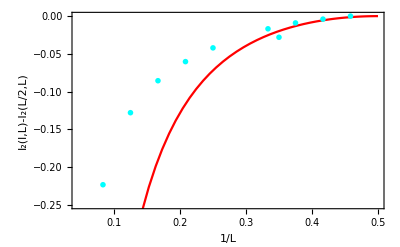

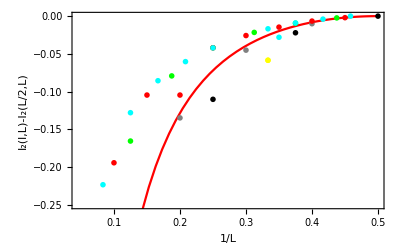

```mathematica
SetDirectory[NotebookDirectory[]];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Red}];
(***************)
marker1=Graphics[{Disk[]}];
data6={{2/6,-0.05843671}};
l6=ListPlot[data6,PlotStyle->Yellow,PlotMarkers->{marker1,.03}];
fit6=FindFit[data6,J[c,x],{c},x]
Show[pactual,l6,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=6"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
data8={{2/8,-0.11014749},{3/8,-0.02205001},{4/8,0}};
l8=ListPlot[data8,PlotStyle->Black,PlotMarkers->{marker1,.03}];
fit8=FindFit[data8,J[c,x],{c},x]
Show[pactual,l8,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=8"}}]
(*aaaaaaaaaaaaaaaaaaaaa*)
data10={{2/10,-0.13474265 },{3/10,-0.04504970},{4/10,-0.01002948}};
l10=ListPlot[data10,PlotStyle->Gray,PlotMarkers->{marker1,.03}];
fit10=FindFit[data10,J[c,x],{c},x]
Show[pactual,l10,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=10"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
data16={{2/16,-0.16540133},{3/16,-0.07915012},{4/16,-0.04189553},{5/16,-0.02155202},{6/16,-0.00947486},{7/16,-0.00235248}};
l16=ListPlot[data16,PlotStyle->Green,PlotMarkers->{marker1,.03}];
fit16=FindFit[data16,J[c,x],{c},x]
Show[pactual,l16,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=16"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
data20={{2/20,-0.19417424},{3/20,-0.10450639},{4/20,-0.10450639},{5/20,-0.04190940},{6/20,-0.02572357},{7/20,-0.01456808},{8/20,-0.00656855},{9/20,-0.00205329}};
l20=ListPlot[data20,PlotStyle->Red,PlotMarkers->{marker1,.03}];
fit20=FindFit[data20,J[c,x],{c},x]
Show[pactual,l20,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=20"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
data24={{2/24,-0.22323951},{3/24,-0.12787162},{4/24,-0.08552056},{5/24,-0.06024982},{6/24,-0.04203786},{7/20,-0.02800167},{8/24,-0.01678355},{9/24,-0.00901948},{10/24,-0.00396543},{11/24,0}};
l24=ListPlot[data24,PlotStyle->Cyan,PlotMarkers->{marker1,.03}];
fit24=FindFit[data24,J[c,x],{c},x]
Show[pactual,l24,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=24"}}]
(*********************)
Show[pactual,l6,l8,l10,l16,l20,l24,PlotRange->{-0.25,0},Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L",None}}]
```